# Числено решаване на обикновени диференциални уравнения

Дадени са следните задачи: (a и b са съответно предпоследната и последната цифра от факултетния номер)
a) y' = y - (2 + a)sinx, y(b) = a + b, x ∈ [b; b + 0.5]
б) y' = y - ln(x^2 + 1) + (2x)/(x^2 + 1) + b, y(a) = a + b, x ∈ [a; a + 0.1]
1. Да се намерят точните решения.
2. Да се решат по методите: Ойлер, модифициран Ойлер, Рунге-Кута (1, 1), Рунге-Кута (2/3, 2/3), Рунге-Кута с 4 междинни точки за а) при h = 0.1, 
за б) при n = 5. Да се направи сравнение между точното решение и численото приближение. Да се представи геометрична интерпретация на резултатите.
3. Колко би трябвало да са n и h за всеки един от посочените методи за всяка от задачите, за да се достигне точност за а) 10^-4, за б) 10^-7?

## Решение на а)

### 1. Да се намерят точните решения

Търсим общо решение:

```mathematica
Clear[x, y]
DSolve[y'[x] ==y[x] - 8Sin[x], y[x], x]
```

{{y[x]→ⅇ^x C[1]+4 (Cos[x]+Sin[x])}}

Търсим частно решение:

```mathematica
Clear[x, y]
DSolve[{y'[x] ==y[x] - 8Sin[x], y[7] == 13}, y[x], x]
```

{{y[x]→(13 ⅇ^x-4 ⅇ^x Cos[7]+4 ⅇ^7 Cos[x]-4 ⅇ^x Sin[7]+4 ⅇ^7 Sin[x])/ⅇ^7}}

Визуализация на точното решение

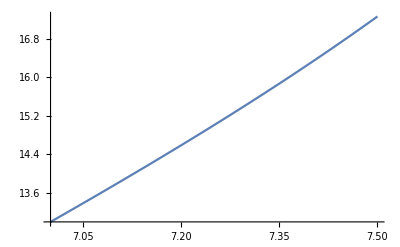

```mathematica
yt[x_] := (13 ⅇ^x-4 ⅇ^x Cos[7]+4 ⅇ^7 Cos[x]-4 ⅇ^x Sin[7]+4 ⅇ^7 Sin[x])/ⅇ^7
Plot[yt[x], {x, 7,7.5}]
```

Извод: Не можем да намерим точно решение с аналитичен метод

### 2. Да се реши по методите: Ойлер, модифициран Ойлер, Рунге-Кута (1, 1), Рунге-Кута (2/3, 2/3), Рунге-Кута с 4 междинни точки при h = 0.1:

#### 2.1. Ойлер

Мрежата е с n = 5. и стъпка h = 0.1

Теоретичната локална грешка  е 0.01

Теоретичната глобална грешка е 0.1

i = 0 x_i = 7. y_i = 13. f_i = 7.74411 y_точно = 13. Истинска грешка = 1.77636×10^-15

i = 1 x_i = 7.1 y_i = 13.7744 f_i = 7.94266 y_точно = 13.7842 Истинска грешка = 0.00978072

i = 2 x_i = 7.2 y_i = 14.5687 f_i = 8.21933 y_точно = 14.5933 Истинска грешка = 0.0245819

i = 3 x_i = 7.3 y_i = 15.3906 f_i = 8.58712 y_точно = 15.4362 Истинска грешка = 0.0456081

i = 4 x_i = 7.4 y_i = 16.2493 f_i = 9.05966 y_точно = 16.3235 Истинска грешка = 0.0742258

i = 5 x_i = 7.5 y_i = 17.1553 f_i = 9.65129 y_точно = 17.2673 Истинска грешка = 0.111981

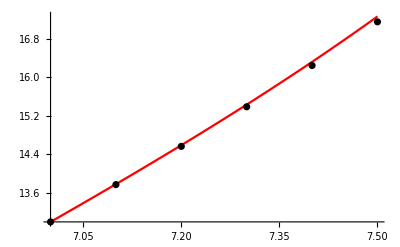

```mathematica
(*Въвеждаме услонието на задачата*)
a = 7.;b=7.5;
x = a;
y =13.;
points = {{x,y}};
f[x_,y_] := y - 8Sin[x]
(*Точно решение*)
yt[x_] := (13 ⅇ^x-4 ⅇ^x Cos[7]+4 ⅇ^7 Cos[x]-4 ⅇ^x Sin[7]+4 ⅇ^7 Sin[x])/ⅇ^7
(*Съставяме мрежата*)
h = 0.1; n = (b - a)/h;
Print["Мрежата е с n = ", n , " и стъпка h = ", h]
(*Изчисляваме теоретичната грешка*)
Print["Теоретичната локална грешка  е ", h^2]
Print["Теоретичната глобална грешка е ", h]
(*Намираме неизвестните стойности за Subscript[y, i]*)
For[i = 0, i  <= n, i++,
Print["i = ", i, " x_i = ", x, " y_i = ", y, " f_i = ", f[x,y] , " y_(:0442:043e:0447:043d:043e) = ", yt[x], " Истинска грешка = ", Abs[y-yt[x]]];
y = y + h*f[x,y];
x = x + h;
AppendTo[points, {x,y}]
]
(*Визуализация на резултатите*)
gryt = Plot[yt[x], {x, a, b}, PlotStyle->Red];
grp = ListPlot[points, PlotStyle->Black];
Show[gryt, grp]
```

#### 2.2. Модифициран метод на Ойлер

Мрежата е с n = 5. и стъпка h = 0.1

Теоретичната локална грешка  е 0.001

Теоретичната глобална грешка е 0.01

i = 0 x_i = 7. y_i = 13. f_i = 7.74411 x_(i + 1/2) = 7.05 y_(i + 1/2) = 13.3872 f_(i + 1/2) = 7.83645  y_точно = 13. Истинска грешка = 1.77636×10^-15

i = 1 x_i = 7.1 y_i = 13.7836 f_i = 7.95189 x_(i + 1/2) = 7.15 y_(i + 1/2) = 14.1812 f_(i + 1/2) = 8.08307  y_точно = 13.7842 Истинска грешка = 0.000546865

i = 2 x_i = 7.2 y_i = 14.592 f_i = 8.24261 x_(i + 1/2) = 7.25 y_(i + 1/2) = 15.0041 f_(i + 1/2) = 8.41944  y_точно = 14.5933 Истинска грешка = 0.0013068

i = 3 x_i = 7.3 y_i = 15.4339 f_i = 8.6304 x_(i + 1/2) = 7.35 y_(i + 1/2) = 15.8654 f_(i + 1/2) = 8.86008  y_точно = 15.4362 Истинска грешка = 0.00232294

i = 4 x_i = 7.4 y_i = 16.3199 f_i = 9.13024 x_(i + 1/2) = 7.45 y_(i + 1/2) = 16.7764 f_(i + 1/2) = 9.42039  y_точно = 16.3235 Истинска грешка = 0.00364414

i = 5 x_i = 7.5 y_i = 17.2619 f_i = 9.75794 x_(i + 1/2) = 7.55 y_(i + 1/2) = 17.7498 f_(i + 1/2) = 10.1166  y_точно = 17.2673 Истинска грешка = 0.00532559

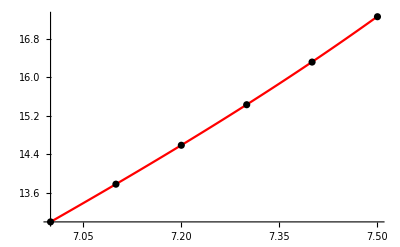

```mathematica
(*Въвеждаме услонието на задачата*)
a = 7.;b=7.5;
x = a;
y =13.;
points = {{x,y}};
f[x_,y_] := y - 8Sin[x]
(*Точно решение*)
yt[x_] := (13 ⅇ^x-4 ⅇ^x Cos[7]+4 ⅇ^7 Cos[x]-4 ⅇ^x Sin[7]+4 ⅇ^7 Sin[x])/ⅇ^7
(*Съставяме мрежата*)
h = 0.1; n = (b - a)/h;
Print["Мрежата е с n = ", n , " и стъпка h = ", h]
(*Изчисляваме теоретичната грешка*)
Print["Теоретичната локална грешка  е ", h^3]
Print["Теоретичната глобална грешка е ", h^2]
(*Намираме неизвестните стойности за Subscript[y, i]*)
For[i = 0, i  <= n, i++,
x12 = x + h/2;
y12 = y + h/2 f[x,y];
Print["i = ", i, " x_i = ", x, " y_i = ", y, " f_i = ", f[x,y]  , " x_(i + 1/2) = ", x12, " y_(i + 1/2) = ", y12, " f_(i + 1/2) = ", f[x12,y12]  " y_(:0442:043e:0447:043d:043e) = ", yt[x], " Истинска грешка = ", Abs[y-yt[x]]];
y = y + h*f[x12,y12];
x = x + h;
AppendTo[points, {x,y}]
]
(*Визуализация на резултатите*)
gryt = Plot[yt[x], {x, a,b}, PlotStyle->Red];
grp = ListPlot[points, PlotStyle-> Black];
Show[gryt, grp]
```

#### 2.3. РК32 - Формула (1, 1)

Мрежата е с n = 5. и стъпка h = 0.1

Теоретичната локална грешка  е 0.001

Теоретичната глобална грешка е 0.01

i = 0 x_i = 7. y_i = 13. f_i = 7.74411 k_1 = 0.774411 k_2 = 0.794266 y_точно = 13. Истинска грешка = 1.77636×10^-15

i = 1 x_i = 7.1 y_i = 13.7843 f_i = 7.95259 k_1 = 0.795259 k_2 = 0.823025 y_точно = 13.7842 Истинска грешка = 0.000146835

i = 2 x_i = 7.2 y_i = 14.5935 f_i = 8.24414 k_1 = 0.824414 k_2 = 0.86144 y_точно = 14.5933 Истинска грешка = 0.000221854

i = 3 x_i = 7.3 y_i = 15.4364 f_i = 8.63291 k_1 = 0.863291 k_2 = 0.911003 y_точно = 15.4362 Истинска грешка = 0.000189126

i = 4 x_i = 7.4 y_i = 16.3236 f_i = 9.13389 k_1 = 0.913389 k_2 = 0.973294 y_точно = 16.3235 Истинска грешка = 7.18544×10^-6

i = 5 x_i = 7.5 y_i = 17.2669 f_i = 9.7629 k_1 = 0.97629 k_2 = 1.04998 y_точно = 17.2673 Истинска грешка = 0.000371565

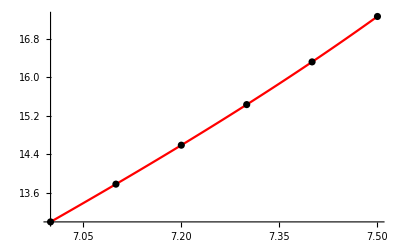

```mathematica
(*Въвеждаме услонието на задачата*)
a = 7.;b=7.5;
x = a;
y =13.;
points = {{x,y}};
f[x_,y_] := y - 8Sin[x]
(*Точно решение*)
yt[x_] := (13 ⅇ^x-4 ⅇ^x Cos[7]+4 ⅇ^7 Cos[x]-4 ⅇ^x Sin[7]+4 ⅇ^7 Sin[x])/ⅇ^7
(*Съставяме мрежата*)
h = 0.1; n = (b - a)/h;
Print["Мрежата е с n = ", n , " и стъпка h = ", h]
(*Изчисляваме теоретичната грешка*)
Print["Теоретичната локална грешка  е ", h^3]
Print["Теоретичната глобална грешка е ", h^2]
(*Намираме неизвестните стойности за Subscript[y, i]*)
For[i = 0, i  <= n, i++,
k1 = h *  f[x,y];
k2 = h *  f[x + h,y + k1];
Print["i = ", i, " x_i = ", x, " y_i = ", y, " f_i = ", f[x,y]  , " k_1 = ", k1, " k_2 = ", k2," y_(:0442:043e:0447:043d:043e) = ", yt[x], " Истинска грешка = ", Abs[y-yt[x]]];
y = y + 1/2(k1+k2);
x = x + h;
AppendTo[points, {x,y}]
]
(*Визуализация на резултатите*)
gryt = Plot[yt[x], {x, a, b}, PlotStyle->Red];
grp = ListPlot[points, PlotStyle->Black];
Show[gryt, grp]
```

#### 2.4. РК32 - Формула (2/3, 2/3)

Мрежата е с n = 5. и стъпка h = 0.1

Теоретичната локална грешка  е 0.001

Теоретичната глобална грешка е 0.01

i = 0 x_i = 7. y_i = 13. f_i = 7.74411 k_1 = 0.774411 k_2 = 0.787027 y_точно = 13. Истинска грешка = 1.77636×10^-15

i = 1 x_i = 7.1 y_i = 13.7839 f_i = 7.95212 k_1 = 0.795212 k_2 = 0.81304 y_точно = 13.7842 Истинска грешка = 0.000318288

i = 2 x_i = 7.2 y_i = 14.5925 f_i = 8.24311 k_1 = 0.824311 k_2 = 0.848254 y_точно = 14.5933 Истинска грешка = 0.000802567

i = 3 x_i = 7.3 y_i = 15.4347 f_i = 8.63123 k_1 = 0.863123 k_2 = 0.894139 y_точно = 15.4362 Истинска грешка = 0.00149356

i = 4 x_i = 7.4 y_i = 16.3211 f_i = 9.13145 k_1 = 0.913145 k_2 = 0.952246 y_точно = 16.3235 Истинска грешка = 0.00243761

i = 5 x_i = 7.5 y_i = 17.2636 f_i = 9.75958 k_1 = 0.975958 k_2 = 1.02422 y_точно = 17.2673 Истинска грешка = 0.00368738

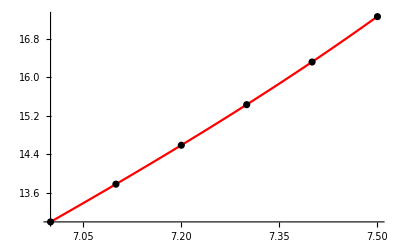

```mathematica
(*Въвеждаме услонието на задачата*)
a = 7.;b=7.5;
x = a;
y =13.;
points = {{x,y}};
f[x_,y_] := y - 8Sin[x]
(*Точно решение*)
yt[x_] := (13 ⅇ^x-4 ⅇ^x Cos[7]+4 ⅇ^7 Cos[x]-4 ⅇ^x Sin[7]+4 ⅇ^7 Sin[x])/ⅇ^7
(*Съставяме мрежата*)
h = 0.1; n = (b - a)/h;
Print["Мрежата е с n = ", n , " и стъпка h = ", h]
(*Изчисляваме теоретичната грешка*)
Print["Теоретичната локална грешка  е ", h^3]
Print["Теоретичната глобална грешка е ", h^2]
(*Намираме неизвестните стойности за Subscript[y, i]*)
For[i = 0, i  <= n, i++,
k1 = h *  f[x,y];
k2 = h *  f[x + 2/3*h,y + 2/3* k1];
Print["i = ", i, " x_i = ", x, " y_i = ", y, " f_i = ", f[x,y]  , " k_1 = ", k1, " k_2 = ", k2," y_(:0442:043e:0447:043d:043e) = ", yt[x], " Истинска грешка = ", Abs[y-yt[x]]];
y = y +1/4*k1 + 3/4 *k2;
x = x + h;
AppendTo[points, {x,y}]
]
(*Визуализация на резултатите*)
gryt = Plot[yt[x], {x, a, b}, PlotStyle->Red];
grp = ListPlot[points, PlotStyle->Black];
Show[gryt, grp]
```

#### 2.5. РК54 - Формула с четири междинни точки

Мрежата е с n = 5. и стъпка h = 0.1

Теоретичната локална грешка  е 0.00001

Теоретичната глобална грешка е 0.0001

i = 0 x_i = 7. y_i = 13. f_i = 7.74411 k_1 = 0.774411 k_2 = 0.783645 k_3 = 0.784106 k_4 = 0.795235 y_точно = 13. Истинска грешка = 1.77636×10^-15

i = 1 x_i = 7.1 y_i = 13.7842 f_i = 7.95244 k_1 = 0.795244 k_2 = 0.808364 k_3 = 0.80902 k_4 = 0.824387 y_точно = 13.7842 Истинска грешка = 1.41331×10^-7

i = 2 x_i = 7.2 y_i = 14.5933 f_i = 8.24392 k_1 = 0.824392 k_2 = 0.842081 k_3 = 0.842965 k_4 = 0.863273 y_точно = 14.5933 Истинска грешка = 3.45098×10^-7

i = 3 x_i = 7.3 y_i = 15.4362 f_i = 8.63272 k_1 = 0.863272 k_2 = 0.886252 k_3 = 0.887401 k_4 = 0.913395 y_точно = 15.4362 Истинска грешка = 6.29757×10^-7

i = 4 x_i = 7.4 y_i = 16.3235 f_i = 9.13388 k_1 = 0.913388 k_2 = 0.942422 k_3 = 0.943873 k_4 = 0.976342 y_точно = 16.3235 Истинска грешка = 1.01656×10^-6

i = 5 x_i = 7.5 y_i = 17.2673 f_i = 9.76327 k_1 = 0.976327 k_2 = 1.01222 k_3 = 1.01402 k_4 = 1.05379 y_точно = 17.2673 Истинска грешка = 1.52989×10^-6

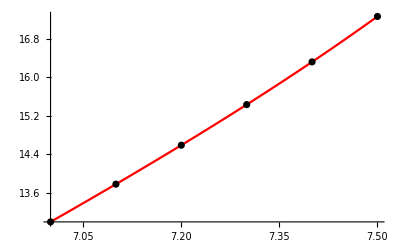

```mathematica
a = 7.;b=7.5;
x = a;
y =13.;
points = {{x,y}};
f[x_,y_] := y - 8Sin[x]
(*Точно решение*)
yt[x_] := (13 ⅇ^x-4 ⅇ^x Cos[7]+4 ⅇ^7 Cos[x]-4 ⅇ^x Sin[7]+4 ⅇ^7 Sin[x])/ⅇ^7
(*Съставяме мрежата*)
h = 0.1; n = (b - a)/h;
Print["Мрежата е с n = ", n , " и стъпка h = ", h]
(*Изчисляваме теоретичната грешка*)
Print["Теоретичната локална грешка  е ", h^5]
Print["Теоретичната глобална грешка е ", h^4]
(*Намираме неизвестните стойности за Subscript[y, i]*)
For[i = 0, i  <= n, i++,
k1 = h *  f[x,y];
k2 = h *  f[x + h/2,y + k1/2];
k3 = h *  f[x + h/2,y + k2/2];
k4 = h *  f[x + h,y + k3];
Print["i = ", i, " x_i = ", x, " y_i = ", y, " f_i = ", f[x,y]  , " k_1 = ", k1, " k_2 = ", k2, " k_3 = ", k3, " k_4 = ", k4, " y_(:0442:043e:0447:043d:043e) = ", yt[x], " Истинска грешка = ", Abs[y-yt[x]]];
y = y +1/6(k1 + 2k2 + 2k3 + k4);
x = x + h;
AppendTo[points, {x,y}]
]
(*Визуализация на резултатите*)
gryt = Plot[yt[x], {x, a, b}, PlotStyle->Red];
grp = ListPlot[points, PlotStyle->Black];
Show[gryt, grp]
```

### 3. Колко би трябвало да са n и h за всеки един от посочените методи, за да се достигне точност 10^-4

#### 2.1. Ойлер

```mathematica
a = 7.;b=7.5;
Clear[n]
Reduce[(b-a)/n <= 10^-4]
```

Reduce::ratnz: Reduce was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

n<0||n≥5000.

```mathematica
(*Въвеждаме услонието на задачата*)
a = 7.;b=7.5;
x = a;
y =13.;
points = {{x,y}};
f[x_,y_] := y - 8Sin[x]
(*Точно решение*)
yt[x_] := (13 ⅇ^x-4 ⅇ^x Cos[7]+4 ⅇ^7 Cos[x]-4 ⅇ^x Sin[7]+4 ⅇ^7 Sin[x])/ⅇ^7
(*Съставяме мрежата*)
n= 5000; h = (b - a)/n;
Print["Мрежата е с n = ", n , " и стъпка h = ", h]
(*Изчисляваме теоретичната грешка*)
Print["Теоретичната локална грешка  е ", h^2]
Print["Теоретичната глобална грешка е ", h]
```

Мрежата е с n = 5000 и стъпка h = 0.0001

Теоретичната локална грешка  е 1.×10^-8

Теоретичната глобална грешка е 0.0001

#### 2.2. Модифициран метод на Ойлер

```mathematica
a = 7.;b=7.5;
Clear[n]
Reduce[(b-a)/n <= 10^-4]
```

Reduce::ratnz: Reduce was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

n<0||n≥5000.

```mathematica
(*Въвеждаме услонието на задачата*)
a = 7.;b=7.5;
x = a;
y =13.;
points = {{x,y}};
f[x_,y_] := y - 8Sin[x]
(*Точно решение*)
yt[x_] := (13 ⅇ^x-4 ⅇ^x Cos[7]+4 ⅇ^7 Cos[x]-4 ⅇ^x Sin[7]+4 ⅇ^7 Sin[x])/ⅇ^7
(*Съставяме мрежата*)
n= 5000; h = (b - a)/n;
Print["Мрежата е с n = ", n , " и стъпка h = ", h]
(*Изчисляваме теоретичната грешка*)
Print["Теоретичната локална грешка  е ", h^3]
Print["Теоретичната глобална грешка е ", h^2]
```

Мрежата е с n = 5000 и стъпка h = 0.0001

Теоретичната локална грешка  е 1.×10^-12

Теоретичната глобална грешка е 1.×10^-8

#### 2.3. РК32 - Формула (1, 1)

```mathematica
Clear[n]
Reduce[((b-a)/n)^2 <= 10^-4,n]
```

Reduce::ratnz: Reduce was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

n≤-50.||n≥50.

```mathematica
(*Въвеждаме услонието на задачата*)
a = 7.;b=7.5;
x = a;
y =13.;
points = {{x,y}};
f[x_,y_] := y - 8Sin[x]
(*Точно решение*)
yt[x_] := (13 ⅇ^x-4 ⅇ^x Cos[7]+4 ⅇ^7 Cos[x]-4 ⅇ^x Sin[7]+4 ⅇ^7 Sin[x])/ⅇ^7
(*Съставяме мрежата*)
n = 50; h = (b - a)/n;
Print["Мрежата е с n = ", n , " и стъпка h = ", h]
(*Изчисляваме теоретичната грешка*)
Print["Теоретичната локална грешка  е ", h^3]
Print["Теоретичната глобална грешка е ", h^2]
```

Мрежата е с n = 50 и стъпка h = 0.01

Теоретичната локална грешка  е 1.×10^-6

Теоретичната глобална грешка е 0.0001

#### 2.4. РК32 - Формула (2/3, 2/3)

```mathematica
Clear[n]
Reduce[((b-a)/n)^2 <= 10^-4,n]
```

Reduce::ratnz: Reduce was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

n≤-50.||n≥50.

```mathematica
(*Въвеждаме услонието на задачата*)
a = 7.;b=7.5;
x = a;
y =13.;
points = {{x,y}};
f[x_,y_] := y - 8Sin[x]
(*Точно решение*)
yt[x_] := (13 ⅇ^x-4 ⅇ^x Cos[7]+4 ⅇ^7 Cos[x]-4 ⅇ^x Sin[7]+4 ⅇ^7 Sin[x])/ⅇ^7
(*Съставяме мрежата*)
n = 50; h = (b - a)/n;
Print["Мрежата е с n = ", n , " и стъпка h = ", h]
(*Изчисляваме теоретичната грешка*)
Print["Теоретичната локална грешка  е ", h^3]
Print["Теоретичната глобална грешка е ", h^2]
```

Мрежата е с n = 50 и стъпка h = 0.01

Теоретичната локална грешка  е 1.×10^-6

Теоретичната глобална грешка е 0.0001

#### 2.5. РК54 - Формула с четири междинни точки

```mathematica
Clear[n]
Reduce[((b-a)/n)^4 <= 10^-4, n]
```

Reduce::ratnz: Reduce was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

n≤-5.||n≥5.

```mathematica
a = 7.;b=7.5;
x = a;
y =13.;
points = {{x,y}};
f[x_,y_] := y - 8Sin[x]
(*Точно решение*)
yt[x_] := (13 ⅇ^x-4 ⅇ^x Cos[7]+4 ⅇ^7 Cos[x]-4 ⅇ^x Sin[7]+4 ⅇ^7 Sin[x])/ⅇ^7
(*Съставяме мрежата*)
n = 5; h = (b - a)/n;
Print["Мрежата е с n = ", n , " и стъпка h = ", h]
(*Изчисляваме теоретичната грешка*)
Print["Теоретичната локална грешка  е ", h^5]
Print["Теоретичната глобална грешка е ", h^4]
```

Мрежата е с n = 5 и стъпка h = 0.1

Теоретичната локална грешка  е 0.00001

Теоретичната глобална грешка е 0.0001

## Решение на б)

### 1. Да се намерят точните решения

Търсим общо решение:

```mathematica
Clear[x, y]
DSolve[y'[x] ==y[x] - Log[x^2 + 1] + (2x)/(x^2 + 1) + 7, y[x], x]
```

{{y[x]→-7+ⅇ^x C[1]+Log[1+x^2]}}

Търсим частно решение:

```mathematica
Clear[x, y]
DSolve[{y'[x] ==y[x] - Log[x^2 + 1] + (2x)/(x^2 + 1) + 7, y[6] == 13}, y[x], x]
```

{{y[x]→(-7 ⅇ^6+20 ⅇ^x-ⅇ^x Log[37]+ⅇ^6 Log[1+x^2])/ⅇ^6}}

Визуализация на точното решение

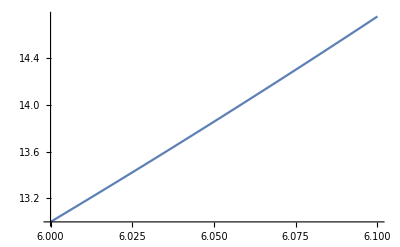

```mathematica
yt[x_] := (-7 ⅇ^6+20 ⅇ^x-ⅇ^x Log[37]+ⅇ^6 Log[1+x^2])/ⅇ^6
Plot[yt[x], {x,6,6.1}]
```

Извод: Не можем да намерим точно решение с аналитичен метод

### 2. Да се реши по методите: Ойлер, модифициран Ойлер, Рунге-Кута (1, 1), Рунге-Кута (2/3, 2/3), Рунге-Кута с 4 междинни точки при n = 5:

#### 2.1. Ойлер

Мрежата е с n = 5 и стъпка h = 0.02

Теоретичната локална грешка  е 0.0004

Теоретичната глобална грешка е 0.02

i = 0 x_i = 6. y_i = 13. f_i = 16.7134 y_точно = 13. Истинска грешка = 0.

i = 1 x_i = 6.02 y_i = 13.3343 f_i = 17.0402 y_точно = 13.3376 Истинска грешка = 0.00328957

i = 2 x_i = 6.04 y_i = 13.6751 f_i = 17.3735 y_точно = 13.6818 Истинска грешка = 0.00671166

i = 3 x_i = 6.06 y_i = 14.0225 f_i = 17.7135 y_точно = 14.0328 Истинска грешка = 0.0102703

i = 4 x_i = 6.08 y_i = 14.3768 f_i = 18.0604 y_точно = 14.3908 Истинска грешка = 0.0139695

i = 5 x_i = 6.1 y_i = 14.738 f_i = 18.4142 y_точно = 14.7558 Истинска грешка = 0.0178135

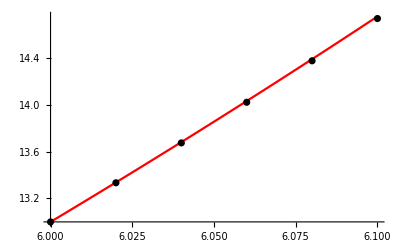

```mathematica
(*Въвеждаме услонието на задачата*)
a = 6.;b=6.1;
x = a;
y =13.;
points = {{x,y}};
f[x_,y_] := y- Log[x^2 + 1] + (2x)/(x^2 + 1) + 7
(*Точно решение*)
yt[x_] := (-7 ⅇ^6+20 ⅇ^x-ⅇ^x Log[37]+ⅇ^6 Log[1+x^2])/ⅇ^6
(*Съставяме мрежата*)
n = 5; h = (b - a)/n;
Print["Мрежата е с n = ", n , " и стъпка h = ", h]
(*Изчисляваме теоретичната грешка*)
Print["Теоретичната локална грешка  е ", h^2]
Print["Теоретичната глобална грешка е ", h]
(*Намираме неизвестните стойности за Subscript[y, i]*)
For[i = 0, i  <= n, i++,
Print["i = ", i, " x_i = ", x, " y_i = ", y, " f_i = ", f[x,y] , " y_(:0442:043e:0447:043d:043e) = ", yt[x], " Истинска грешка = ", Abs[y-yt[x]]];
y = y + h*f[x,y];
x = x + h;
AppendTo[points, {x,y}]
]
(*Визуализация на резултатите*)
gryt = Plot[yt[x], {x, a, b}, PlotStyle->Red];
grp = ListPlot[points, PlotStyle->Black];
Show[gryt, grp]
```

#### 2.2. Модифициран метод на Ойлер

Мрежата е с n = 5 и стъпка h = 0.02

Теоретичната локална грешка  е 8.×10^-6

Теоретичната глобална грешка е 0.0004

i = 0 x_i = 6. y_i = 13. f_i = 16.7134 x_(i + 1/2) = 6.01 y_(i + 1/2) = 13.1671 f_(i + 1/2) = 16.8768  y_точно = 13. Истинска грешка = 0.

i = 1 x_i = 6.02 y_i = 13.3375 f_i = 17.0434 x_(i + 1/2) = 6.03 y_(i + 1/2) = 13.508 f_(i + 1/2) = 17.2101  y_точно = 13.3376 Истинска грешка = 0.0000219159

i = 2 x_i = 6.04 y_i = 13.6817 f_i = 17.3802 x_(i + 1/2) = 6.05 y_(i + 1/2) = 13.8555 f_(i + 1/2) = 17.5503  y_точно = 13.6818 Истинска грешка = 0.0000447185

i = 3 x_i = 6.06 y_i = 14.0327 f_i = 17.7237 x_(i + 1/2) = 6.07 y_(i + 1/2) = 14.21 f_(i + 1/2) = 17.8973  y_точно = 14.0328 Истинска грешка = 0.0000684345

i = 4 x_i = 6.08 y_i = 14.3907 f_i = 18.0743 x_(i + 1/2) = 6.09 y_(i + 1/2) = 14.5714 f_(i + 1/2) = 18.2513  y_точно = 14.3908 Истинска грешка = 0.0000930916

i = 5 x_i = 6.1 y_i = 14.7557 f_i = 18.4319 x_(i + 1/2) = 6.11 y_(i + 1/2) = 14.94 f_(i + 1/2) = 18.6125  y_точно = 14.7558 Истинска грешка = 0.000118718

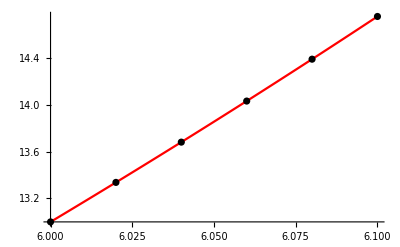

```mathematica
(*Въвеждаме услонието на задачата*)
a = 6.;b=6.1;
x = a;
y =13.;
points = {{x,y}};
f[x_,y_] := y- Log[x^2 + 1] + (2x)/(x^2 + 1) + 7
(*Точно решение*)
yt[x_] := (-7 ⅇ^6+20 ⅇ^x-ⅇ^x Log[37]+ⅇ^6 Log[1+x^2])/ⅇ^6
(*Съставяме мрежата*)
n = 5; h = (b - a)/n;
Print["Мрежата е с n = ", n , " и стъпка h = ", h]
(*Изчисляваме теоретичната грешка*)
Print["Теоретичната локална грешка  е ", h^3]
Print["Теоретичната глобална грешка е ", h^2]
(*Намираме неизвестните стойности за Subscript[y, i]*)
For[i = 0, i  <= n, i++,
x12 = x + h/2;
y12 = y + h/2 f[x,y];
Print["i = ", i, " x_i = ", x, " y_i = ", y, " f_i = ", f[x,y]  , " x_(i + 1/2) = ", x12, " y_(i + 1/2) = ", y12, " f_(i + 1/2) = ", f[x12,y12]  " y_(:0442:043e:0447:043d:043e) = ", yt[x], " Истинска грешка = ", Abs[y-yt[x]]];
y = y + h*f[x12,y12];
x = x + h;
AppendTo[points, {x,y}]
]
(*Визуализация на резултатите*)
gryt = Plot[yt[x], {x, a,b}, PlotStyle->Red];
grp = ListPlot[points, PlotStyle-> Black];
Show[gryt, grp]
```

#### 2.3. РК32 - Формула (1, 1)

```mathematica
(*Въвеждаме услонието на задачата*)
a = 6.;b=6.1;
x = a;
y =13.;
points = {{x,y}};
f[x_,y_] := y- Log[x^2 + 1] + (2x)/(x^2 + 1) + 7
(*Точно решение*)
yt[x_] := (-7 ⅇ^6+20 ⅇ^x-ⅇ^x Log[37]+ⅇ^6 Log[1+x^2])/ⅇ^6
(*Съставяме мрежата*)
n = 5; h = (b - a)/n;
Print["Мрежата е с n = ", n , " и стъпка h = ", h]
(*Изчисляваме теоретичната грешка*)
Print["Теоретичната локална грешка  е ", h^3]
Print["Теоретичната глобална грешка е ", h^2]
(*Намираме неизвестните стойности за Subscript[y, i]*)
For[i = 0, i  <= n, i++,
k1 = h *  f[x,y];
k2 = h *  f[x + h,y + k1];
Print["i = ", i, " x_i = ", x, " y_i = ", y, " f_i = ", f[x,y]  , " k_1 = ", k1, " k_2 = ", k2," y_(:0442:043e:0447:043d:043e) = ", yt[x], " Истинска грешка = ", Abs[y-yt[x]]];
y = y + 1/2(k1+k2);
x = x + h;
AppendTo[points, {x,y}]
]
(*Визуализация на резултатите*)
gryt = Plot[yt[x], {x, a, b}, PlotStyle->Red];
grp = ListPlot[points, PlotStyle->Black];
Show[gryt, grp]
```

Мрежата е с n = 5 и стъпка h = 0.02

Теоретичната локална грешка  е 8.×10^-6

Теоретичната глобална грешка е 0.0004

i = 0 x_i = 6. y_i = 13. f_i = 16.7134 k_1 = 0.334268 k_2 = 0.340804 y_точно = 13. Истинска грешка = 0.

i = 1 x_i = 6.02 y_i = 13.3375 f_i = 17.0434 k_1 = 0.340869 k_2 = 0.347537 y_точно = 13.3376 Истинска грешка = 0.0000218494

i = 2 x_i = 6.04 y_i = 13.6817 f_i = 17.3802 k_1 = 0.347604 k_2 = 0.354407 y_точно = 13.6818 Истинска грешка = 0.0000445845

i = 3 x_i = 6.06 y_i = 14.0327 f_i = 17.7237 k_1 = 0.354475 k_2 = 0.361416 y_точно = 14.0328 Истинска грешка = 0.0000682322

i = 4 x_i = 6.08 y_i = 14.3907 f_i = 18.0743 k_1 = 0.361485 k_2 = 0.368567 y_точно = 14.3908 Истинска грешка = 0.00009282

i = 5 x_i = 6.1 y_i = 14.7557 f_i = 18.4319 k_1 = 0.368638 k_2 = 0.375864 y_точно = 14.7558 Истинска грешка = 0.000118376

-Graphics-

#### 2.4. РК32 - Формула (2/3, 2/3)

```mathematica
(*Въвеждаме услонието на задачата*)
a = 6.;b=6.1;
x = a;
y =13.;
points = {{x,y}};
f[x_,y_] := y- Log[x^2 + 1] + (2x)/(x^2 + 1) + 7
(*Точно решение*)
yt[x_] := (-7 ⅇ^6+20 ⅇ^x-ⅇ^x Log[37]+ⅇ^6 Log[1+x^2])/ⅇ^6
(*Съставяме мрежата*)
n = 5; h = (b - a)/n;
Print["Мрежата е с n = ", n , " и стъпка h = ", h]
(*Изчисляваме теоретичната грешка*)
Print["Теоретичната локална грешка  е ", h^3]
Print["Теоретичната глобална грешка е ", h^2]
(*Намираме неизвестните стойности за Subscript[y, i]*)
For[i = 0, i  <= n, i++,
k1 = h *  f[x,y];
k2 = h *  f[x + 2/3*h,y + 2/3* k1];
Print["i = ", i, " x_i = ", x, " y_i = ", y, " f_i = ", f[x,y]  , " k_1 = ", k1, " k_2 = ", k2," y_(:0442:043e:0447:043d:043e) = ", yt[x], " Истинска грешка = ", Abs[y-yt[x]]];
y = y +1/4*k1 + 3/4 *k2;
x = x + h;
AppendTo[points, {x,y}]
]
(*Визуализация на резултатите*)
gryt = Plot[yt[x], {x, a, b}, PlotStyle->Red];
grp = ListPlot[points, PlotStyle->Black];
Show[gryt, grp]
```

Мрежата е с n = 5 и стъпка h = 0.02

Теоретичната локална грешка  е 8.×10^-6

Теоретичната глобална грешка е 0.0004

i = 0 x_i = 6. y_i = 13. f_i = 16.7134 k_1 = 0.334268 k_2 = 0.338625 y_точно = 13. Истинска грешка = 0.

i = 1 x_i = 6.02 y_i = 13.3375 f_i = 17.0434 k_1 = 0.340869 k_2 = 0.345314 y_точно = 13.3376 Истинска грешка = 0.0000218937

i = 2 x_i = 6.04 y_i = 13.6817 f_i = 17.3802 k_1 = 0.347604 k_2 = 0.352139 y_точно = 13.6818 Истинска грешка = 0.0000446738

i = 3 x_i = 6.06 y_i = 14.0327 f_i = 17.7237 k_1 = 0.354475 k_2 = 0.359102 y_точно = 14.0328 Истинска грешка = 0.000068367

i = 4 x_i = 6.08 y_i = 14.3907 f_i = 18.0743 k_1 = 0.361485 k_2 = 0.366207 y_точно = 14.3908 Истинска грешка = 0.000093001

i = 5 x_i = 6.1 y_i = 14.7557 f_i = 18.4319 k_1 = 0.368638 k_2 = 0.373455 y_точно = 14.7558 Истинска грешка = 0.000118604

-Graphics-

#### 2.5. РК54 - Формула с четири междинни точки

Мрежата е с n = 5 и стъпка h = 0.02

Теоретичната локална грешка  е 3.2×10^-9

Теоретичната глобална грешка е 1.6×10^-7

i = 0 x_i = 6. y_i = 13. f_i = 16.7134 k_1 = 0.334268 k_2 = 0.337536 k_3 = 0.337568 k_4 = 0.34087 y_точно = 13. Истинска грешка = 0.

i = 1 x_i = 6.02 y_i = 13.3376 f_i = 17.0435 k_1 = 0.340869 k_2 = 0.344203 k_3 = 0.344237 k_4 = 0.347605 y_точно = 13.3376 Истинска грешка = 4.36579×10^-10

i = 2 x_i = 6.04 y_i = 13.6818 f_i = 17.3802 k_1 = 0.347604 k_2 = 0.351006 k_3 = 0.35104 k_4 = 0.354476 y_точно = 13.6818 Истинска грешка = 8.90847×10^-10

i = 3 x_i = 6.06 y_i = 14.0328 f_i = 17.7238 k_1 = 0.354476 k_2 = 0.357947 k_3 = 0.357981 k_4 = 0.361488 y_точно = 14.0328 Истинска грешка = 1.36335×10^-9

i = 4 x_i = 6.08 y_i = 14.3908 f_i = 18.0744 k_1 = 0.361487 k_2 = 0.365028 k_3 = 0.365064 k_4 = 0.368641 y_точно = 14.3908 Истинска грешка = 1.85462×10^-9

i = 5 x_i = 6.1 y_i = 14.7558 f_i = 18.432 k_1 = 0.368641 k_2 = 0.372253 k_3 = 0.372289 k_4 = 0.375939 y_точно = 14.7558 Истинска грешка = 2.36523×10^-9

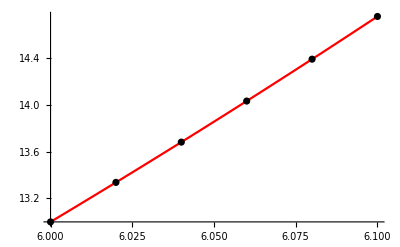

```mathematica
(*Въвеждаме услонието на задачата*)
a = 6.;b=6.1;
x = a;
y =13.;
points = {{x,y}};
f[x_,y_] := y- Log[x^2 + 1] + (2x)/(x^2 + 1) + 7
(*Точно решение*)
yt[x_] := (-7 ⅇ^6+20 ⅇ^x-ⅇ^x Log[37]+ⅇ^6 Log[1+x^2])/ⅇ^6
(*Съставяме мрежата*)
n = 5; h = (b - a)/n;
Print["Мрежата е с n = ", n , " и стъпка h = ", h]
(*Изчисляваме теоретичната грешка*)
Print["Теоретичната локална грешка  е ", h^5]
Print["Теоретичната глобална грешка е ", h^4]
(*Намираме неизвестните стойности за Subscript[y, i]*)
For[i = 0, i  <= n, i++,
k1 = h *  f[x,y];
k2 = h *  f[x + h/2,y + k1/2];
k3 = h *  f[x + h/2,y + k2/2];
k4 = h *  f[x + h,y + k3];
Print["i = ", i, " x_i = ", x, " y_i = ", y, " f_i = ", f[x,y]  , " k_1 = ", k1, " k_2 = ", k2, " k_3 = ", k3, " k_4 = ", k4, " y_(:0442:043e:0447:043d:043e) = ", yt[x], " Истинска грешка = ", Abs[y-yt[x]]];
y = y +1/6(k1 + 2k2 + 2k3 + k4);
x = x + h;
AppendTo[points, {x,y}]
]
(*Визуализация на резултатите*)
gryt = Plot[yt[x], {x, a, b}, PlotStyle->Red];
grp = ListPlot[points, PlotStyle->Black];
Show[gryt, grp]
```

### 3. Колко би трябвало да са n и h за всеки един от посочените методи, за да се достигне точност 10^-7

#### 2.1. Ойлер

```mathematica
a = 6.;b=6.1;
Clear[n]
Reduce[(b-a)/n <= 10^-7]
```

Reduce::ratnz: Reduce was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

n<0||n≥1.×10^6

```mathematica
(*Въвеждаме услонието на задачата*)
a = 6.;b=6.1;
x = a;
y =13.;
points = {{x,y}};
f[x_,y_] := y- Log[x^2 + 1] + (2x)/(x^2 + 1) + 7
(*Точно решение*)
yt[x_] := (-7 ⅇ^6+20 ⅇ^x-ⅇ^x Log[37]+ⅇ^6 Log[1+x^2])/ⅇ^6
(*Съставяме мрежата*)
n = 10^6; h = (b - a)/n;
Print["Мрежата е с n = ", n , " и стъпка h = ", h]
(*Изчисляваме теоретичната грешка*)
Print["Теоретичната локална грешка  е ", h^2]
Print["Теоретичната глобална грешка е ", h]
```

Мрежата е с n = 1000000 и стъпка h = 1.×10^-7

Теоретичната локална грешка  е 1.×10^-14

Теоретичната глобална грешка е 1.×10^-7

#### 2.2. Модифициран метод на Ойлер

```mathematica
a = 6.;b=6.1;
Clear[n]
Reduce[(b-a)/n <= 10^-7]
```

Reduce::ratnz: Reduce was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

n<0||n≥1.×10^6

```mathematica
(*Въвеждаме услонието на задачата*)
a = 6.;b=6.1;
x = a;
y =13.;
points = {{x,y}};
f[x_,y_] := y- Log[x^2 + 1] + (2x)/(x^2 + 1) + 7
(*Точно решение*)
yt[x_] := (-7 ⅇ^6+20 ⅇ^x-ⅇ^x Log[37]+ⅇ^6 Log[1+x^2])/ⅇ^6
(*Съставяме мрежата*)
n = 10^6; h = (b - a)/n;
Print["Мрежата е с n = ", n , " и стъпка h = ", h]
(*Изчисляваме теоретичната грешка*)
Print["Теоретичната локална грешка  е ", h^3]
Print["Теоретичната глобална грешка е ", h^2]
```

Мрежата е с n = 1000000 и стъпка h = 1.×10^-7

Теоретичната локална грешка  е 1.×10^-21

Теоретичната глобална грешка е 1.×10^-14

#### 2.3. РК32 - Формула (1, 1)

```mathematica
Clear[n]
Reduce[((b-a)/n)^2 <= 10^-7,n]
```

Reduce::ratnz: Reduce was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

n≤-316.228||n≥316.228

```mathematica
(*Въвеждаме услонието на задачата*)
a = 6.;b=6.1;
x = a;
y =13.;
points = {{x,y}};
f[x_,y_] := y- Log[x^2 + 1] + (2x)/(x^2 + 1) + 7
(*Точно решение*)
yt[x_] := (-7 ⅇ^6+20 ⅇ^x-ⅇ^x Log[37]+ⅇ^6 Log[1+x^2])/ⅇ^6
(*Съставяме мрежата*)
n = 317; h = (b - a)/n;
Print["Мрежата е с n = ", n , " и стъпка h = ", h]
(*Изчисляваме теоретичната грешка*)
Print["Теоретичната локална грешка  е ", h^3]
Print["Теоретичната глобална грешка е ", h^2]
```

Мрежата е с n = 317 и стъпка h = 0.000315457

Теоретичната локална грешка  е 3.13922×10^-11

Теоретичната глобална грешка е 9.95134×10^-8

#### 2.4. РК32 - Формула (2/3, 2/3)

```mathematica
Clear[n]
Reduce[((b-a)/n)^2 <= 10^-7,n]
```

Reduce::ratnz: Reduce was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

n≤-316.228||n≥316.228

```mathematica
(*Въвеждаме услонието на задачата*)
a = 6.;b=6.1;
x = a;
y =13.;
points = {{x,y}};
f[x_,y_] := y- Log[x^2 + 1] + (2x)/(x^2 + 1) + 7
(*Точно решение*)
yt[x_] := (-7 ⅇ^6+20 ⅇ^x-ⅇ^x Log[37]+ⅇ^6 Log[1+x^2])/ⅇ^6
(*Съставяме мрежата*)
n = 317; h = (b - a)/n;
Print["Мрежата е с n = ", n , " и стъпка h = ", h]
(*Изчисляваме теоретичната грешка*)
Print["Теоретичната локална грешка  е ", h^3]
Print["Теоретичната глобална грешка е ", h^2]
```

Мрежата е с n = 317 и стъпка h = 0.000315457

Теоретичната локална грешка  е 3.13922×10^-11

Теоретичната глобална грешка е 9.95134×10^-8

#### 2.5. РК54 - Формула с четири междинни точки

```mathematica
Clear[n]
Reduce[((b-a)/n)^4 <= 10^-7, n]
```

Reduce::ratnz: Reduce was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

n≤-5.62341||n≥5.62341

```mathematica
(*Въвеждаме услонието на задачата*)
a = 6.;b=6.1;
x = a;
y =13.;
points = {{x,y}};
f[x_,y_] := y- Log[x^2 + 1] + (2x)/(x^2 + 1) + 7
(*Точно решение*)
yt[x_] := (-7 ⅇ^6+20 ⅇ^x-ⅇ^x Log[37]+ⅇ^6 Log[1+x^2])/ⅇ^6
(*Съставяме мрежата*)
n = 6; h = (b - a)/n;
Print["Мрежата е с n = ", n , " и стъпка h = ", h]
(*Изчисляваме теоретичната грешка*)
Print["Теоретичната локална грешка  е ", h^5]
Print["Теоретичната глобална грешка е ", h^4]
```

Мрежата е с n = 6 и стъпка h = 0.0166667

Теоретичната локална грешка  е 1.28601×10^-9

Теоретичната глобална грешка е 7.71605×10^-8